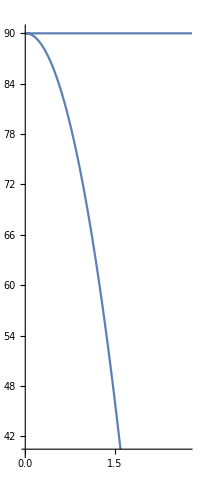

```mathematica
f1[t_] := t/2;
f2[t_] := 90+t/5-9.8*t^2/2;
(*Animate[ParametricPlot[{f1[t], f2[t]},{t, 0, tt}], {tt, 0, 3.2}]*)
ParametricPlot[{f1[t], f2[t]},{t, 0, 3.2}]
```

```mathematica
Integrate[Sqrt[f1'[t]^2+f2'[t]^2],{t}]
```

Integrate::ilim: Invalid integration variable or limit(s) in {t}.

```mathematica
Integrate[-9.8,t]
```

-9.8 t

```mathematica
f1[t_] := 3*Cos[t]+ Cos[3*t];
f2[t_] := 3*Sin[t] - Sin[3*t];
curves = ParametricPlot[{f1[t], f2[t]}, {t,0, 2*Pi}];
Animate[
Show[
curves,
Graphics[{PointSize[Large],Point[{f1[t],f2[t]}]}]
],{t,0,2 Pi}]
integral = Integrate[2*Pi*f2[t]*Sqrt[f1'[t]^2+f2'[t]^2], {t, 0, pi}];
Real[integral]
```

Real[ConditionalExpression[48/5 π Sin[pi]^3 √(Sin[2 pi]^2) Tan[pi], 2 Re[pi]≤π||pi∉ℝ]]

```mathematica
f1[t_] := Cos[2*Pi*t];
f2[t_] := Sin[2*Pi*t];
curves2 = ParametricPlot[{f1[t], f2[t]}, {t,0, 1/2}];
Animate[
Show[
curves2,
Graphics[{PointSize[Large],Point[{f1[t],f2[t]}]}]
],{t,0,1/2}]
```

```mathematica
f1[t_] := Cos[2*Pi*t^2];
f2[t_] := Sin[2*Pi*t^2];
curves3 = ParametricPlot[{f1[t], f2[t]}, {t,0, 1/2}];
Animate[
Show[
curves3,
Graphics[{PointSize[Large],Point[{f1[t],f2[t]}]}]
],{t,0,1/2}]
```

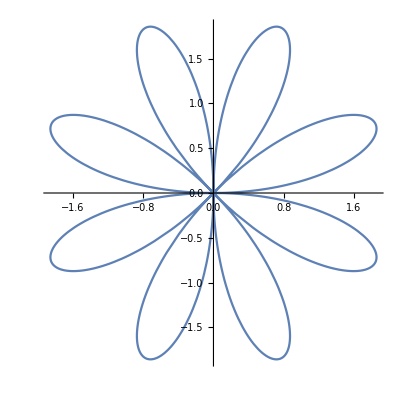

```mathematica
PolarPlot[2*Sin[4*t], {t,0, 2*Pi}]
```

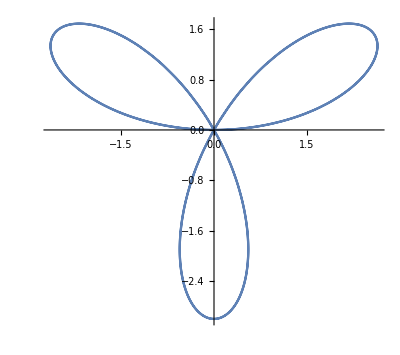

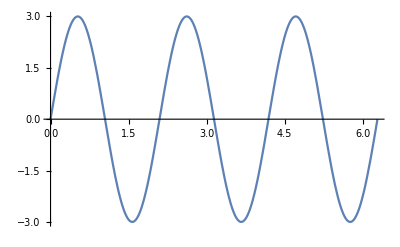

```mathematica
PolarPlot[3*Sin[3*t], {t,0, 2*Pi}]
Plot[3*Sin[3*t], {t,0, 2*Pi}]
```